```mathematica
Needs["ExperimentEvaluation`"]
```

## Experiments I

```mathematica
data=readAllFiles[{"20110803/GP4D_1000","GPAT4D_SSM_500"},labels,ReplaceParamValues->{"FC55"->"ZFC55"}];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
data=readAllFiles[(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GP_MAZE_MAP*"])~Join~(StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"])~Join~{"GPATGP_MAZE_ALL"},labels];
```

```mathematica
names=Flatten@Transpose@{{"GP_MAZE_MAP2_ORIG","GP_MAZE_MAP2_RF4","GP_MAZE_MAP2_RF8","GP_MAZE_MAP2_NOVER","GP_MAZE_MAP3_ORIG","GP_MAZE_MAP3_RF4","GP_MAZE_MAP3_RF8","GP_MAZE_MAP3_NOVER"},{"GPAT_MAZE_MAP2_ORIG","GPAT_MAZE_MAP2_RF4","GPAT_MAZE_MAP2_RF8","GPAT_MAZE_MAP2_NOVER","GPAT_MAZE_MAP3_ORIG","GPAT_MAZE_MAP3_RF4","GPAT_MAZE_MAP3_RF8","GPAT_MAZE_MAP3_NOVER"}};
```

```mathematica
labels={"GP_MAP2_NOVER","GP_MAP2_ORIG","GP_MAP2_RF4","GP_MAP2_RF8","GP_MAP3_NOVER","GP_MAP3_ORIG","GP_MAP3_RF4","GP_MAP3_RF8","GP_MAP4_NOVER","GP_MAP4_ORIG","GP_MAP4_RF4","GP_MAP4_RF8","GPAT_MAP2_NOVER","GPAT_MAP2_ORIG","GPAT_MAP2_RF4","GPAT_MAP2_RF8","GPAT_MAP3_NOVER","GPAT_MAP3_ORIG","GPAT_MAP3_RF4","GPAT_MAP3_RF8","GPAT_MAP4_NOVER","GPAT_MAP4_ORIG","GPAT_MAP4_RF4","GATP_MAP4_RF8","GPATGP_MAP2_ORIG","GPATGP_MAP2_NOVER","GPATGP_MAP2_RF4","GPATGP_MAP2_RF8","GPATGP_MAP3_ORIG","GPATGP_MAP3_NOVER","GPATGP_MAP3_RF4","GPATGP_MAP3_RF8","GPATGP_MAP24_ORIG","GPATGP_MAP4_NOVER","GPATGP_MAP4_RF4","GPATGP_MAP4_RF8"};
```

```mathematica
data=readAllFiles[names,labels];
```

```mathematica
listAllFiles[{"GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"}]
```

{{/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/experiments_010.txt,/Users/drchaj1/java/exp/GP_4D_FC55_1000_old/parameters_010.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_001.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_001.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_002.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_002.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_003.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_003.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_004.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_004.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_005.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_005.txt},{/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/experiments_006.txt,/Users/drchaj1/java/exp/GPAT_4D_FC55_ALL/parameters_006.txt}}

```mathematica
names={"GP_MAP2_200_old","GPAT_MAP2_ALL","GP_2D_H_1000_old","GPAT_2D_H_ALL","GP_4D_F_1000_old","GPAT_4D_F_ALL","GP_4D_FC55_1000_old","GPAT_4D_FC55_ALL"};
labels=Flatten[Outer[StringJoin[#2,#1]&,{"MAP2","2D_H","4D_F","4D_FC55"},{"GP_","GPAT_BASIC_","GPAT_RANDOM_","GPAT_CONSTANT1_","GPAT_SIMPLE_","GPAT_SIMPLE_REC_","GPAT_SIMPLE_REC2_","GPAT_SIMPLE_REC3_","GPAT_SIMPLE_ROOTO_","GPAT_SIMPLE_REC4_","GPAT_SIMPLE_SIMPLE2_","GPAT_SIMPLE_REC5_"}]];
data=readAllFiles[names,labels];
```

```mathematica
StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPAT_MAZE_MAP*"]
```

{GPAT_MAZE_MAP2_NOVER,GPAT_MAZE_MAP2_ORIG,GPAT_MAZE_MAP2_RF4,GPAT_MAZE_MAP2_RF8,GPAT_MAZE_MAP3_NOVER,GPAT_MAZE_MAP3_ORIG,GPAT_MAZE_MAP3_RF4,GPAT_MAZE_MAP3_RF8,GPAT_MAZE_MAP4_NOVER,GPAT_MAZE_MAP4_ORIG,GPAT_MAZE_MAP4_RF4,GPAT_MAZE_MAP4_RF8}

```mathematica
keepOnlyBest[StringReplace[#,"~/java/exp/"->""]&/@FileNames["~/java/exp/GPATGP_MAZE_ALL"],"BSF",60]
```

```mathematica
changingParameters[data]
```

{GPAT.FUNCTION_IMPL,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,SOLVER,SYMBOLIC_REGRESSION_4D.F}

```mathematica
sortedData = data;
```

```mathematica
sortedData=sortDataByParams[data,{"SYMBOLIC_REGRESSION_4D.F"},ReplaceParamValues->{"ZFC55"->"FC55"}];
```

```mathematica
data=readAllFiles[{"GPAT_4D_FC55_ALL","A"}];
```

```mathematica
saveData[data,"B"]
```

```mathematica
printAsTable[sortedData,{"SOLVER","MAZE.MAP","SYMBOLIC_REGRESSION_4D.F","GP.TARGET_FITNESS","GP.TYPE","GPAT.FUNCTION_IMPL","GPAT.MUTATION_HEAVY_PROB","GPAT.MUTATION_HEAVY_POWER","GPAT.SPECIES_SIZE_MEAN"}]
```

ID | PARAM FILE | SOLVER | MAZE.MAP | SYMBOLIC_REGRESSION_4D.F | GP.TARGET_FITNESS | GP.TYPE | GPAT.FUNCTION_IMPL | GPAT.MUTATION_HEAVY_PROB | GPAT.MUTATION_HEAVY_POWER | GPAT.SPECIES_SIZE_MEAN
GP_MAP2 | GP_MAP2_200_old/parameters_001.txt | GP | map2.csv | NONE | 50. | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_MAP2 | GPAT_MAP2_ALL/parameters_001.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_MAP2 | GPAT_MAP2_ALL/parameters_002.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_MAP2 | GPAT_MAP2_ALL/parameters_003.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_MAP2 | GPAT_MAP2_ALL/parameters_004.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_MAP2 | GPAT_MAP2_ALL/parameters_005.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_MAP2 | GPAT_MAP2_ALL/parameters_006.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_MAP2 | GPAT_MAP2_ALL/parameters_007.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_MAP2 | GPAT_MAP2_ALL/parameters_008.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_MAP2 | GPAT_MAP2_ALL/parameters_009.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_MAP2 | GPAT_MAP2_ALL/parameters_010.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_MAP2 | GPAT_MAP2_ALL/parameters_011.txt | GPAT | map2.csv | NONE | 40. | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_2D_H | GP_2D_H_1000_old/parameters_008.txt | GP | NONE | NONE | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_2D_H | GPAT_2D_H_ALL/parameters_001.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_2D_H | GPAT_2D_H_ALL/parameters_002.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_2D_H | GPAT_2D_H_ALL/parameters_003.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_2D_H | GPAT_2D_H_ALL/parameters_004.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_2D_H | GPAT_2D_H_ALL/parameters_005.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_2D_H | GPAT_2D_H_ALL/parameters_006.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_2D_H | GPAT_2D_H_ALL/parameters_007.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_2D_H | GPAT_2D_H_ALL/parameters_008.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_2D_H | GPAT_2D_H_ALL/parameters_009.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_2D_H | GPAT_2D_H_ALL/parameters_010.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_2D_H | GPAT_2D_H_ALL/parameters_011.txt | GPAT | NONE | NONE | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_F | GP_4D_F_1000_old/parameters_006.txt | GP | NONE | F | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_F | GPAT_4D_F_ALL/parameters_001.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_F | GPAT_4D_F_ALL/parameters_002.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_F | GPAT_4D_F_ALL/parameters_003.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_F | GPAT_4D_F_ALL/parameters_004.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_F | GPAT_4D_F_ALL/parameters_005.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_F | GPAT_4D_F_ALL/parameters_006.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_F | GPAT_4D_F_ALL/parameters_007.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_F | GPAT_4D_F_ALL/parameters_008.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_F | GPAT_4D_F_ALL/parameters_009.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_F | GPAT_4D_F_ALL/parameters_010.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_F | GPAT_4D_F_ALL/parameters_011.txt | GPAT | NONE | F | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GP_4D_FC55 | GP_4D_FC55_1000_old/parameters_010.txt | GP | NONE | FC55 | 0.95 | gp.GP | NONE | NONE | NONE | NONE
GPAT_BASIC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_001.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_RANDOM_4D_FC55 | GPAT_4D_FC55_ALL/parameters_002.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_CONSTANT1_4D_FC55 | GPAT_4D_FC55_ALL/parameters_003.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_4D_FC55 | GPAT_4D_FC55_ALL/parameters_004.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC_4D_FC55 | GPAT_4D_FC55_ALL/parameters_005.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_006.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC3_4D_FC55 | GPAT_4D_FC55_ALL/parameters_007.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_ROOTO_4D_FC55 | GPAT_4D_FC55_ALL/parameters_008.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC4_4D_FC55 | GPAT_4D_FC55_ALL/parameters_009.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_SIMPLE2_4D_FC55 | GPAT_4D_FC55_ALL/parameters_010.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.
GPAT_SIMPLE_REC5_4D_FC55 | GPAT_4D_FC55_ALL/parameters_011.txt | GPAT | NONE | FC55 | 0.95 | gpat.GPAT | gpat.ATFunctions$ | 0. | 1 | 20.

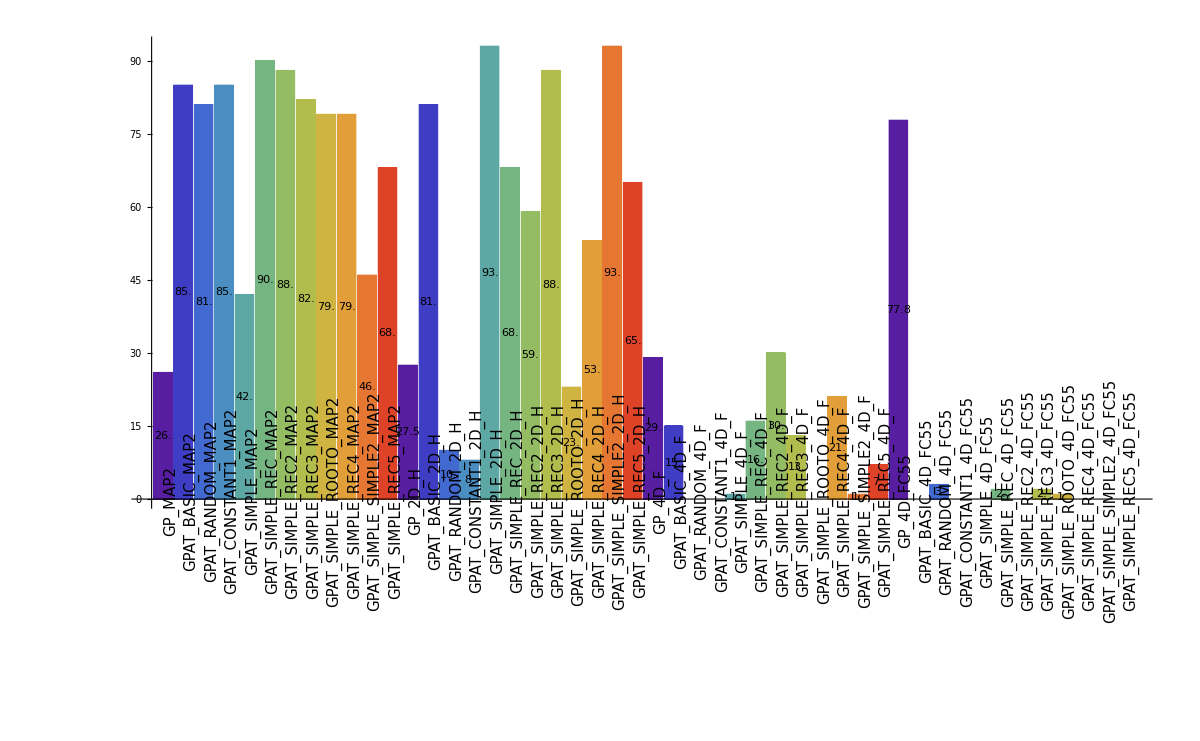

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",12]
```

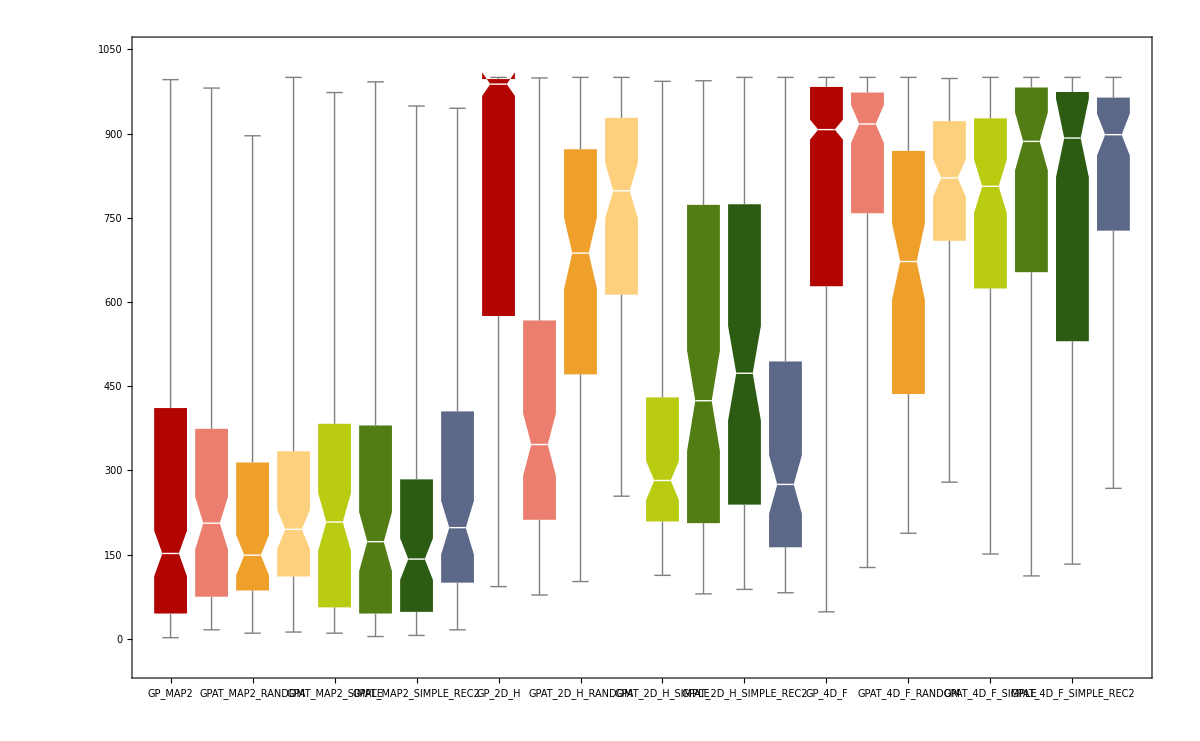

```mathematica
plotAsBoxWhiskerChart[sortedData,"BSFG",8]
```

## Experiments II

```mathematica
names={"GPAT_2D-1_REC7PAR","GPAT_maze-1_REC7PAR","GPAT_maze-2_REC7PAR"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE","GPAT.DISTANCE_REC5_C1","GPAT.DISTANCE_REC5_C2"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE_REC5_C1,GPAT.DISTANCE_REC5_C2,GP.TARGET_FITNESS,ID,MAZE.MAP,PROBLEM,SYMBOLIC_REGRESSION.F}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GPAT_2D_I_SIMPLE_REC7_0.1_0.1 | GPAT_2D-1_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.1_0.5 | GPAT_2D-1_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.1_0.8 | GPAT_2D-1_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.1_0.9 | GPAT_2D-1_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.1_0.95 | GPAT_2D-1_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.5_0.1 | GPAT_2D-1_REC7PAR/parameters_016.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.5_0.5 | GPAT_2D-1_REC7PAR/parameters_019.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.5_0.8 | GPAT_2D-1_REC7PAR/parameters_022.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.5_0.9 | GPAT_2D-1_REC7PAR/parameters_025.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.5_0.95 | GPAT_2D-1_REC7PAR/parameters_028.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.9_0.1 | GPAT_2D-1_REC7PAR/parameters_031.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.9_0.5 | GPAT_2D-1_REC7PAR/parameters_034.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.9_0.8 | GPAT_2D-1_REC7PAR/parameters_037.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.9_0.9 | GPAT_2D-1_REC7PAR/parameters_040.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7_0.9_0.95 | GPAT_2D-1_REC7PAR/parameters_043.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.1_0.1 | GPAT_2D-1_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.1_0.5 | GPAT_2D-1_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.1_0.8 | GPAT_2D-1_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.1_0.9 | GPAT_2D-1_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.1_0.95 | GPAT_2D-1_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.5_0.1 | GPAT_2D-1_REC7PAR/parameters_017.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.5_0.5 | GPAT_2D-1_REC7PAR/parameters_020.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.5_0.8 | GPAT_2D-1_REC7PAR/parameters_023.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.5_0.9 | GPAT_2D-1_REC7PAR/parameters_026.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.5_0.95 | GPAT_2D-1_REC7PAR/parameters_029.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.9_0.1 | GPAT_2D-1_REC7PAR/parameters_032.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.9_0.5 | GPAT_2D-1_REC7PAR/parameters_035.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.9_0.8 | GPAT_2D-1_REC7PAR/parameters_038.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.9_0.9 | GPAT_2D-1_REC7PAR/parameters_041.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7_0.9_0.95 | GPAT_2D-1_REC7PAR/parameters_044.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.1_0.1 | GPAT_2D-1_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.1_0.5 | GPAT_2D-1_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.1_0.8 | GPAT_2D-1_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.1_0.9 | GPAT_2D-1_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.1_0.95 | GPAT_2D-1_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.5_0.1 | GPAT_2D-1_REC7PAR/parameters_018.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.5_0.5 | GPAT_2D-1_REC7PAR/parameters_021.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.5_0.8 | GPAT_2D-1_REC7PAR/parameters_024.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.5_0.9 | GPAT_2D-1_REC7PAR/parameters_027.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.5_0.95 | GPAT_2D-1_REC7PAR/parameters_030.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.9_0.1 | GPAT_2D-1_REC7PAR/parameters_033.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.9_0.5 | GPAT_2D-1_REC7PAR/parameters_036.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.9_0.8 | GPAT_2D-1_REC7PAR/parameters_039.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.9_0.9 | GPAT_2D-1_REC7PAR/parameters_042.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7_0.9_0.95 | GPAT_2D-1_REC7PAR/parameters_045.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.1 | GPAT_maze-1_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.5 | GPAT_maze-1_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.8 | GPAT_maze-1_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.9 | GPAT_maze-1_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.1_0.95 | GPAT_maze-1_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.1 | GPAT_maze-1_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.5 | GPAT_maze-1_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.8 | GPAT_maze-1_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.9 | GPAT_maze-1_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.5_0.95 | GPAT_maze-1_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.1 | GPAT_maze-1_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.5 | GPAT_maze-1_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.8 | GPAT_maze-1_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.9 | GPAT_maze-1_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7_0.9_0.95 | GPAT_maze-1_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.1 | GPAT_maze-2_REC7PAR/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.5 | GPAT_maze-2_REC7PAR/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.8 | GPAT_maze-2_REC7PAR/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.9 | GPAT_maze-2_REC7PAR/parameters_004.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.1_0.95 | GPAT_maze-2_REC7PAR/parameters_005.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.1 | GPAT_maze-2_REC7PAR/parameters_006.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.5 | GPAT_maze-2_REC7PAR/parameters_007.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.8 | GPAT_maze-2_REC7PAR/parameters_008.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.9 | GPAT_maze-2_REC7PAR/parameters_009.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.5_0.95 | GPAT_maze-2_REC7PAR/parameters_010.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.1 | GPAT_maze-2_REC7PAR/parameters_011.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.5 | GPAT_maze-2_REC7PAR/parameters_012.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.8 | GPAT_maze-2_REC7PAR/parameters_013.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.9 | GPAT_maze-2_REC7PAR/parameters_014.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7_0.9_0.95 | GPAT_maze-2_REC7PAR/parameters_015.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders

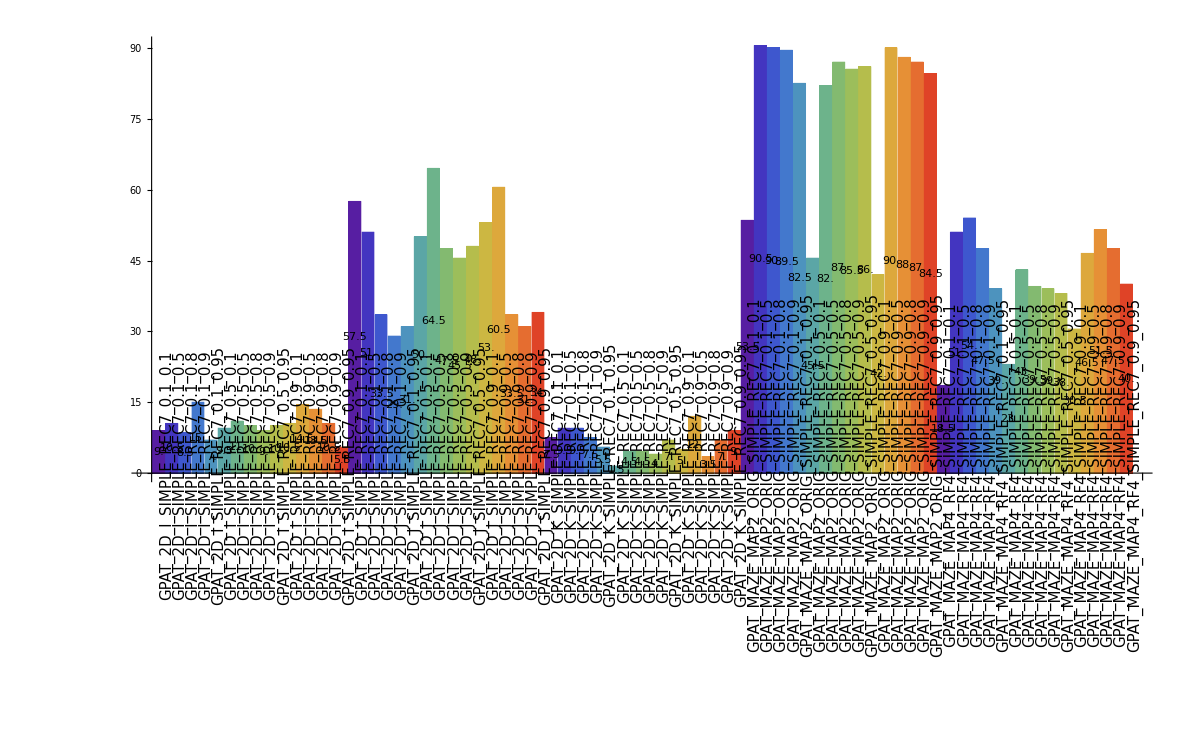

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",15]
```

## Experiments III

```mathematica
names={"GP_1D-1_200","GP_2D-1_200","GP_3D-1_200","GP_4D-1_200","GP_maze-1_200","GP_maze-2_200","GPAT_1D-1_BASE","GPAT_2D-1_BASE","GPAT_3D-1_BASE","GPAT_4D-1_BASE","GPAT_maze-1_BASE","GPAT_maze-2_BASE","GPAT_1D-1_REC_5_6_7","GPAT_2D-1_REC_5_6_7","GPAT_3D-1_REC_5_6_7","GPAT_4D-1_REC_5_6_7","GPAT_maze-1_REC_5_6_7","GPAT_maze-2_REC_5_6_7","GPAT_1D-1_REC_7B","GPAT_2D-1_REC_7B","GPAT_3D-1_REC_7B","GPAT_4D-1_REC_7B","GPAT_maze-1_REC_7B","GPAT_maze-2_REC_7B"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","PROBLEM","GPAT.DISTANCE"},{"ZFC55"->"FC55",RegularExpression["gp.demo.SymbolicRegression.*"]->"","gp.demo.MazeRangeFinders"->"RF4","gp.demo.Maze"->"ORIG","map"->"MAP",".csv"->""}];
changingParameters[data]
```

{GPAT.DISTANCE,GPAT.DISTANCE_REC5_C1,GPAT.DISTANCE_REC5_C2,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","SOLVER","GPAT.DISTANCE","PROBLEM"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","SYMBOLIC_REGRESSION.F","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | SYMBOLIC_REGRESSION.F | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GP_1D_F | GP_1D-1_200/parameters_001.txt | GP | NONE | 1D | F | NONE | NONE | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_F_BASIC | GPAT_1D-1_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | 1D | F | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_F_RANDOM | GPAT_1D-1_BASE/parameters_003.txt | GPAT | gpat.ATFunctions$ | 1D | F | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_F_SIMPLE_REC7 | GPAT_1D-1_REC_5_6_7/parameters_005.txt | GPAT | gpat.ATFunctions$ | 1D | F | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_F_SIMPLE_REC7 | GPAT_1D-1_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | 1D | F | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression
GP_1D_H | GP_1D-1_200/parameters_002.txt | GP | NONE | 1D | H | NONE | NONE | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_H_BASIC | GPAT_1D-1_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | 1D | H | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_H_RANDOM | GPAT_1D-1_BASE/parameters_004.txt | GPAT | gpat.ATFunctions$ | 1D | H | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_H_SIMPLE_REC7 | GPAT_1D-1_REC_5_6_7/parameters_006.txt | GPAT | gpat.ATFunctions$ | 1D | H | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression
GPAT_1D_H_SIMPLE_REC7 | GPAT_1D-1_REC_7B/parameters_002.txt | GPAT | gpat.ATFunctions$ | 1D | H | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression
GP_2D_I | GP_2D-1_200/parameters_001.txt | GP | NONE | 2D | I | NONE | NONE | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_BASIC | GPAT_2D-1_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_RANDOM | GPAT_2D-1_BASE/parameters_004.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7 | GPAT_2D-1_REC_5_6_7/parameters_007.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_I_SIMPLE_REC7 | GPAT_2D-1_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | 2D | I | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GP_2D_J | GP_2D-1_200/parameters_002.txt | GP | NONE | 2D | J | NONE | NONE | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_BASIC | GPAT_2D-1_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_RANDOM | GPAT_2D-1_BASE/parameters_005.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7 | GPAT_2D-1_REC_5_6_7/parameters_008.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_J_SIMPLE_REC7 | GPAT_2D-1_REC_7B/parameters_002.txt | GPAT | gpat.ATFunctions$ | 2D | J | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GP_2D_K | GP_2D-1_200/parameters_003.txt | GP | NONE | 2D | K | NONE | NONE | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_BASIC | GPAT_2D-1_BASE/parameters_003.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_RANDOM | GPAT_2D-1_BASE/parameters_006.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7 | GPAT_2D-1_REC_5_6_7/parameters_009.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GPAT_2D_K_SIMPLE_REC7 | GPAT_2D-1_REC_7B/parameters_003.txt | GPAT | gpat.ATFunctions$ | 2D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression2D
GP_3D_E | GP_3D-1_200/parameters_001.txt | GP | NONE | 3D | E | NONE | NONE | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_E_BASIC | GPAT_3D-1_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | 3D | E | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_E_RANDOM | GPAT_3D-1_BASE/parameters_004.txt | GPAT | gpat.ATFunctions$ | 3D | E | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_E_SIMPLE_REC7 | GPAT_3D-1_REC_5_6_7/parameters_007.txt | GPAT | gpat.ATFunctions$ | 3D | E | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_E_SIMPLE_REC7 | GPAT_3D-1_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | 3D | E | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GP_3D_H | GP_3D-1_200/parameters_002.txt | GP | NONE | 3D | H | NONE | NONE | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_H_BASIC | GPAT_3D-1_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | 3D | H | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_H_RANDOM | GPAT_3D-1_BASE/parameters_005.txt | GPAT | gpat.ATFunctions$ | 3D | H | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_H_SIMPLE_REC7 | GPAT_3D-1_REC_5_6_7/parameters_008.txt | GPAT | gpat.ATFunctions$ | 3D | H | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_H_SIMPLE_REC7 | GPAT_3D-1_REC_7B/parameters_002.txt | GPAT | gpat.ATFunctions$ | 3D | H | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GP_3D_K | GP_3D-1_200/parameters_003.txt | GP | NONE | 3D | K | NONE | NONE | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_K_BASIC | GPAT_3D-1_BASE/parameters_003.txt | GPAT | gpat.ATFunctions$ | 3D | K | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_K_RANDOM | GPAT_3D-1_BASE/parameters_006.txt | GPAT | gpat.ATFunctions$ | 3D | K | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_K_SIMPLE_REC7 | GPAT_3D-1_REC_5_6_7/parameters_009.txt | GPAT | gpat.ATFunctions$ | 3D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GPAT_3D_K_SIMPLE_REC7 | GPAT_3D-1_REC_7B/parameters_003.txt | GPAT | gpat.ATFunctions$ | 3D | K | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression3D
GP_4D_C | GP_4D-1_200/parameters_001.txt | GP | NONE | 4D | C | NONE | NONE | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_C_BASIC | GPAT_4D-1_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | 4D | C | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_C_RANDOM | GPAT_4D-1_BASE/parameters_005.txt | GPAT | gpat.ATFunctions$ | 4D | C | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_C_SIMPLE_REC7 | GPAT_4D-1_REC_5_6_7/parameters_009.txt | GPAT | gpat.ATFunctions$ | 4D | C | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_C_SIMPLE_REC7 | GPAT_4D-1_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | 4D | C | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GP_4D_F | GP_4D-1_200/parameters_002.txt | GP | NONE | 4D | F | NONE | NONE | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_F_BASIC | GPAT_4D-1_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | 4D | F | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_F_RANDOM | GPAT_4D-1_BASE/parameters_006.txt | GPAT | gpat.ATFunctions$ | 4D | F | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_F_SIMPLE_REC7 | GPAT_4D-1_REC_5_6_7/parameters_010.txt | GPAT | gpat.ATFunctions$ | 4D | F | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_F_SIMPLE_REC7 | GPAT_4D-1_REC_7B/parameters_002.txt | GPAT | gpat.ATFunctions$ | 4D | F | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GP_4D_G | GP_4D-1_200/parameters_003.txt | GP | NONE | 4D | G | NONE | NONE | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_G_BASIC | GPAT_4D-1_BASE/parameters_003.txt | GPAT | gpat.ATFunctions$ | 4D | G | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_G_RANDOM | GPAT_4D-1_BASE/parameters_007.txt | GPAT | gpat.ATFunctions$ | 4D | G | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_G_SIMPLE_REC7 | GPAT_4D-1_REC_5_6_7/parameters_011.txt | GPAT | gpat.ATFunctions$ | 4D | G | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_G_SIMPLE_REC7 | GPAT_4D-1_REC_7B/parameters_003.txt | GPAT | gpat.ATFunctions$ | 4D | G | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GP_4D_FC55 | GP_4D-1_200/parameters_004.txt | GP | NONE | 4D | ZFC55 | NONE | NONE | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_FC55_BASIC | GPAT_4D-1_BASE/parameters_004.txt | GPAT | gpat.ATFunctions$ | 4D | ZFC55 | NONE | BASIC | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_FC55_RANDOM | GPAT_4D-1_BASE/parameters_008.txt | GPAT | gpat.ATFunctions$ | 4D | ZFC55 | NONE | RANDOM | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_FC55_SIMPLE_REC7 | GPAT_4D-1_REC_5_6_7/parameters_012.txt | GPAT | gpat.ATFunctions$ | 4D | ZFC55 | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GPAT_4D_FC55_SIMPLE_REC7 | GPAT_4D-1_REC_7B/parameters_004.txt | GPAT | gpat.ATFunctions$ | 4D | ZFC55 | NONE | SIMPLE_REC7 | 0.95 | gp.demo.SymbolicRegression4D
GP_MAZE_MAP2_ORIG | GP_maze-1_200/parameters_001.txt | GP | NONE | MAZE | NONE | map2.csv | NONE | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_BASIC | GPAT_maze-1_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | BASIC | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_RANDOM | GPAT_maze-1_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | RANDOM | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7 | GPAT_maze-1_REC_5_6_7/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GPAT_MAZE_MAP2_ORIG_SIMPLE_REC7 | GPAT_maze-1_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map2.csv | SIMPLE_REC7 | 40. | gp.demo.Maze
GP_MAZE_MAP4_RF4 | GP_maze-2_200/parameters_001.txt | GP | NONE | MAZE | NONE | map4.csv | NONE | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_BASIC | GPAT_maze-2_BASE/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | BASIC | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_RANDOM | GPAT_maze-2_BASE/parameters_002.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | RANDOM | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7 | GPAT_maze-2_REC_5_6_7/parameters_003.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders
GPAT_MAZE_MAP4_RF4_SIMPLE_REC7 | GPAT_maze-2_REC_7B/parameters_001.txt | GPAT | gpat.ATFunctions$ | MAZE | NONE | map4.csv | SIMPLE_REC7 | 40. | gp.demo.MazeRangeFinders

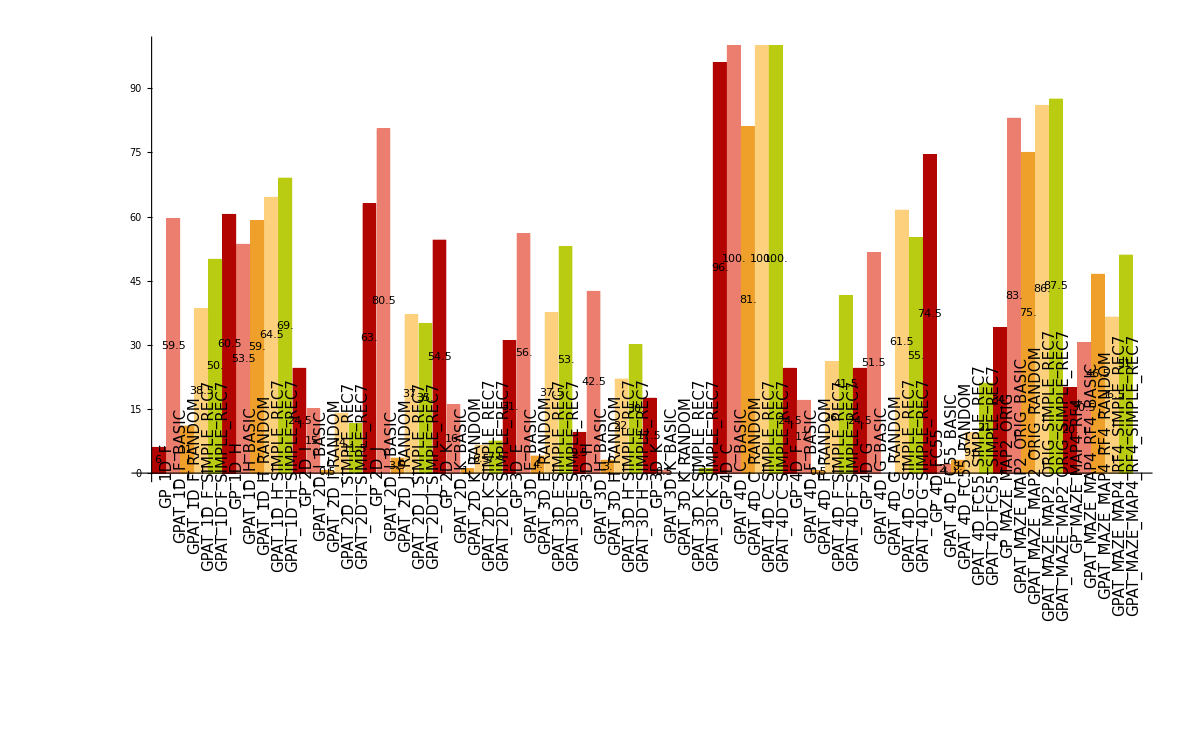

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",5]
```

## Experiments IV

```mathematica
names={"HGPAT_fc55_ALL","HGPAT_reco1D_ALL","HGPAT_xor_ALL","HGP_fc55_ALL","HGP_reco1D_ALL","HGP_xor_ALL"};
data=readAllFiles[names,Null,ReplaceParamValues->{"FC55"->"ZFC55"}];
data=assignLabelsByParameters[data,{"SOLVER","ID","RECO.GENERATOR","GPAT.DISTANCE"},{"ZFC55"->"FC55",RegularExpression["hyper.experiments.reco.problem.PatternGenerator"]->""}];
changingParameters[data]
```

{GPAT.DISTANCE,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TYPE,ID,NET_ACTIVATIONS,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,SOLVER}

```mathematica
(*sdata=selectData[data,{"SOLVER"->"GPAT","GPAT.DISTANCE"->{"SIMPLE_REC5","SIMPLE_REC6","SIMPLE_REC7"}}];*)
(*sdata=removeData[data,{"GPAT.DISTANCE"->{"CONSTANT","ROOTO","SIMPLE","SIMPLE_REC","SIMPLE_REC2","SIMPLE_REC3"}}];*)
sdata=removeData[data,{"GPAT.DISTANCE"->{"SIMPLE2","SIMPLE_REC4","SIMPLE_REC5","SIMPLE_REC6"}}];
sortedData = sortDataByParams[sdata,{"ID","RECO.GENERATOR","SOLVER","GPAT.DISTANCE"}];
printAsTable[sortedData,{"SOLVER","GPAT.FUNCTION_IMPL","ID","RECO.GENERATOR","MAZE.MAP","GPAT.DISTANCE","GP.TARGET_FITNESS","PROBLEM"}]
```

ID | PARAM FILE | SOLVER | GPAT.FUNCTION_IMPL | ID | RECO.GENERATOR | MAZE.MAP | GPAT.DISTANCE | GP.TARGET_FITNESS | PROBLEM
GP_FC | HGP_fc55_ALL/parameters_001.txt | GP | NONE | FC | NONE | NONE | NONE | NONE | FIND_CLUSTER
GPAT_FC_BASIC | HGPAT_fc55_ALL/parameters_001.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | BASIC | NONE | FIND_CLUSTER
GPAT_FC_CONSTANT | HGPAT_fc55_ALL/parameters_002.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | CONSTANT | NONE | FIND_CLUSTER
GPAT_FC_RANDOM | HGPAT_fc55_ALL/parameters_003.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | RANDOM | NONE | FIND_CLUSTER
GPAT_FC_ROOTO | HGPAT_fc55_ALL/parameters_004.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | ROOTO | NONE | FIND_CLUSTER
GPAT_FC_SIMPLE | HGPAT_fc55_ALL/parameters_005.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | SIMPLE | NONE | FIND_CLUSTER
GPAT_FC_SIMPLE_REC | HGPAT_fc55_ALL/parameters_007.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | SIMPLE_REC | NONE | FIND_CLUSTER
GPAT_FC_SIMPLE_REC2 | HGPAT_fc55_ALL/parameters_008.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | SIMPLE_REC2 | NONE | FIND_CLUSTER
GPAT_FC_SIMPLE_REC3 | HGPAT_fc55_ALL/parameters_009.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | SIMPLE_REC3 | NONE | FIND_CLUSTER
GPAT_FC_SIMPLE_REC7 | HGPAT_fc55_ALL/parameters_013.txt | GPAT | gpat.ATFunctions$ | FC | NONE | NONE | SIMPLE_REC7 | NONE | FIND_CLUSTER
GP_RECO1D_CopyMirrored1D | HGP_reco1D_ALL/parameters_001.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | NONE | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_BASIC | HGPAT_reco1D_ALL/parameters_001.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | BASIC | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_CONSTANT | HGPAT_reco1D_ALL/parameters_004.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | CONSTANT | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_RANDOM | HGPAT_reco1D_ALL/parameters_007.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | RANDOM | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_ROOTO | HGPAT_reco1D_ALL/parameters_010.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | ROOTO | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_SIMPLE | HGPAT_reco1D_ALL/parameters_013.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | SIMPLE | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_SIMPLE_REC | HGPAT_reco1D_ALL/parameters_019.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | SIMPLE_REC | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_SIMPLE_REC2 | HGPAT_reco1D_ALL/parameters_022.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | SIMPLE_REC2 | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_SIMPLE_REC3 | HGPAT_reco1D_ALL/parameters_025.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | SIMPLE_REC3 | NONE | RECO
GPAT_RECO1D_CopyMirrored1D_SIMPLE_REC7 | HGPAT_reco1D_ALL/parameters_037.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyMirrored1D | NONE | SIMPLE_REC7 | NONE | RECO
GP_RECO1D_CopyRotated1D | HGP_reco1D_ALL/parameters_003.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | NONE | NONE | RECO
GPAT_RECO1D_CopyRotated1D_BASIC | HGPAT_reco1D_ALL/parameters_003.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | BASIC | NONE | RECO
GPAT_RECO1D_CopyRotated1D_CONSTANT | HGPAT_reco1D_ALL/parameters_006.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | CONSTANT | NONE | RECO
GPAT_RECO1D_CopyRotated1D_RANDOM | HGPAT_reco1D_ALL/parameters_009.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | RANDOM | NONE | RECO
GPAT_RECO1D_CopyRotated1D_ROOTO | HGPAT_reco1D_ALL/parameters_012.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | ROOTO | NONE | RECO
GPAT_RECO1D_CopyRotated1D_SIMPLE | HGPAT_reco1D_ALL/parameters_015.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | SIMPLE | NONE | RECO
GPAT_RECO1D_CopyRotated1D_SIMPLE_REC | HGPAT_reco1D_ALL/parameters_021.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | SIMPLE_REC | NONE | RECO
GPAT_RECO1D_CopyRotated1D_SIMPLE_REC2 | HGPAT_reco1D_ALL/parameters_024.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | SIMPLE_REC2 | NONE | RECO
GPAT_RECO1D_CopyRotated1D_SIMPLE_REC3 | HGPAT_reco1D_ALL/parameters_027.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | SIMPLE_REC3 | NONE | RECO
GPAT_RECO1D_CopyRotated1D_SIMPLE_REC7 | HGPAT_reco1D_ALL/parameters_039.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyRotated1D | NONE | SIMPLE_REC7 | NONE | RECO
GP_RECO1D_CopyShifted1D | HGP_reco1D_ALL/parameters_002.txt | GP | NONE | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | NONE | NONE | RECO
GPAT_RECO1D_CopyShifted1D_BASIC | HGPAT_reco1D_ALL/parameters_002.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | BASIC | NONE | RECO
GPAT_RECO1D_CopyShifted1D_CONSTANT | HGPAT_reco1D_ALL/parameters_005.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | CONSTANT | NONE | RECO
GPAT_RECO1D_CopyShifted1D_RANDOM | HGPAT_reco1D_ALL/parameters_008.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | RANDOM | NONE | RECO
GPAT_RECO1D_CopyShifted1D_ROOTO | HGPAT_reco1D_ALL/parameters_011.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | ROOTO | NONE | RECO
GPAT_RECO1D_CopyShifted1D_SIMPLE | HGPAT_reco1D_ALL/parameters_014.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | SIMPLE | NONE | RECO
GPAT_RECO1D_CopyShifted1D_SIMPLE_REC | HGPAT_reco1D_ALL/parameters_020.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | SIMPLE_REC | NONE | RECO
GPAT_RECO1D_CopyShifted1D_SIMPLE_REC2 | HGPAT_reco1D_ALL/parameters_023.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | SIMPLE_REC2 | NONE | RECO
GPAT_RECO1D_CopyShifted1D_SIMPLE_REC3 | HGPAT_reco1D_ALL/parameters_026.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | SIMPLE_REC3 | NONE | RECO
GPAT_RECO1D_CopyShifted1D_SIMPLE_REC7 | HGPAT_reco1D_ALL/parameters_038.txt | GPAT | gpat.ATFunctions$ | RECO1D | hyper.experiments.reco.problem.PatternGeneratorCopyShifted1D | NONE | SIMPLE_REC7 | NONE | RECO
GP_XOR_XOR | HGP_xor_ALL/parameters_001.txt | GP | NONE | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | NONE | NONE | XOR
GPAT_XOR_XOR_BASIC | HGPAT_xor_ALL/parameters_001.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | BASIC | NONE | XOR
GPAT_XOR_XOR_CONSTANT | HGPAT_xor_ALL/parameters_002.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | CONSTANT | NONE | XOR
GPAT_XOR_XOR_RANDOM | HGPAT_xor_ALL/parameters_003.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | RANDOM | NONE | XOR
GPAT_XOR_XOR_ROOTO | HGPAT_xor_ALL/parameters_004.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | ROOTO | NONE | XOR
GPAT_XOR_XOR_SIMPLE | HGPAT_xor_ALL/parameters_005.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | SIMPLE | NONE | XOR
GPAT_XOR_XOR_SIMPLE_REC | HGPAT_xor_ALL/parameters_007.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | SIMPLE_REC | NONE | XOR
GPAT_XOR_XOR_SIMPLE_REC2 | HGPAT_xor_ALL/parameters_008.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | SIMPLE_REC2 | NONE | XOR
GPAT_XOR_XOR_SIMPLE_REC3 | HGPAT_xor_ALL/parameters_009.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | SIMPLE_REC3 | NONE | XOR
GPAT_XOR_XOR_SIMPLE_REC7 | HGPAT_xor_ALL/parameters_013.txt | GPAT | gpat.ATFunctions$ | XOR | hyper.experiments.reco.problem.PatternGeneratorXOR | NONE | SIMPLE_REC7 | NONE | XOR

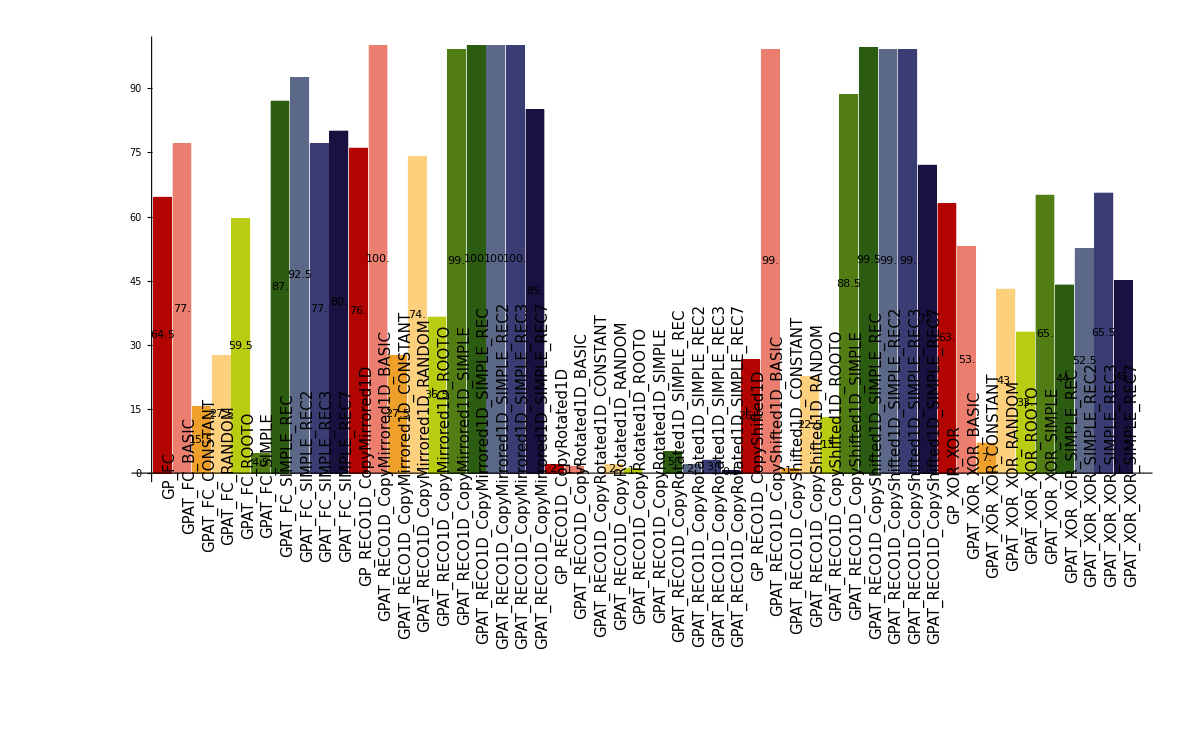

```mathematica
plotBooleanAsBarChart[sortedData,"SUCCESS",10]
```

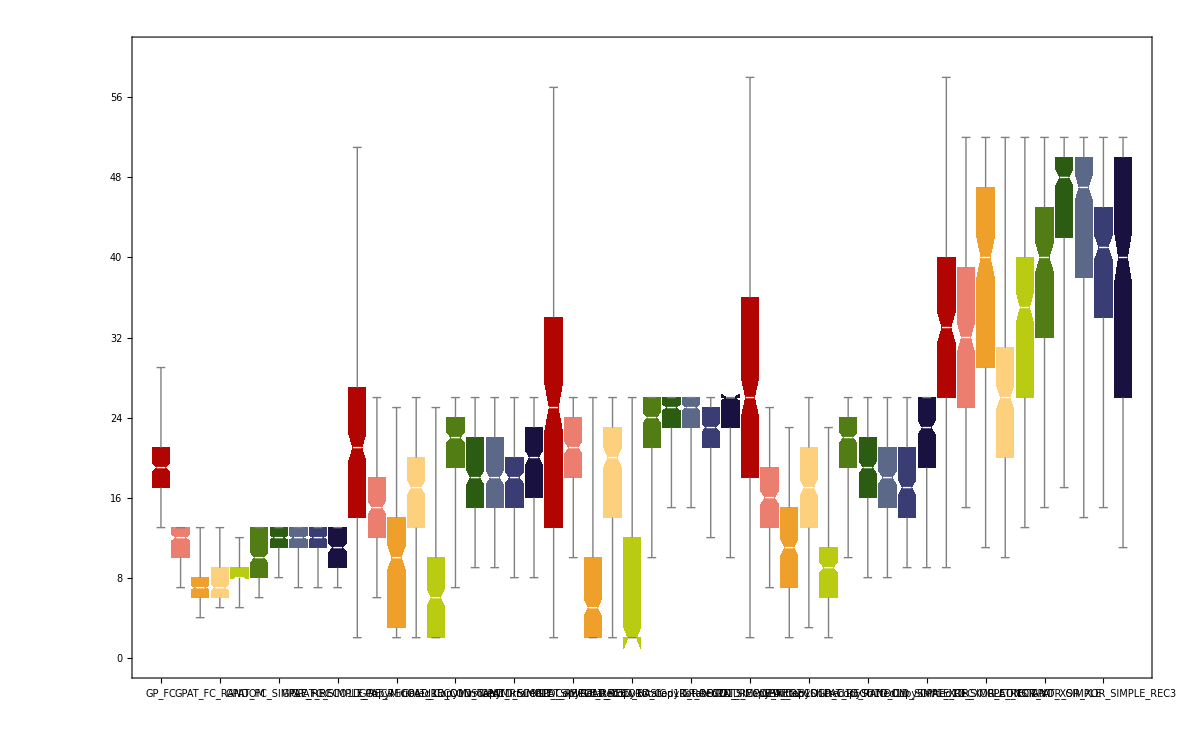

```mathematica
plotAsBoxWhiskerChart[sortedData,"NODES_BSF",10]
```

## Statistics

```mathematica
testMannWhitney[data,"GPAT_H","GPAT_H2","BSF"]
```

median 1: 0.952853

median 2: 0.949325

mean 1: 0.754262

mean 2: 0.528663

variance 1: 0.135817

variance 2: 0.222969

higher/lower variance ratio: 1.64169

U stat: 22636

P-value: 0.0226329

The null hypothesis that the median difference is 0 is rejected at the 5. percent level based on the Mann-Whitney test.

```mathematica
testKruskalWallis[data,{"GP_H","GPAT_H2"},"BSF"]
```

| GPAT_H | GPAT_H2
Mean | 0.754262 | 0.528663
Variance | 0.952853 | 0.949325
Variance | 0.135817 | 0.222969

LocationEquivalenceTest::ntsymmd: The p-value in 1.14305×10^-13, resulting from a test for symmetry, is below 0.05. The tests in {"KruskalWallis"} require that the data is symmetric about a common median.

| Statistic | P-Value
Kruskal-Wallis | 5.19838 | 0.0224202

```mathematica
testFisherExact[{{90,10},{82,18}}]
```

0.152819

```mathematica
testFisherExact[sortedData,"GPAT_E","GPATGP_E","SUCCESS",TwoSided->True,PValueOnly->False]
```

| GPAT_E | GPATGP_E
true | 0. | 1.
false | 200. | 199.
p-value | 1. |

```mathematica
testFisherExactAll[sortedData,"SUCCESS",0.05,TwoSided->True]
```

| 2 | 3 | 4 | 5 | 6
1 | 0.0900213 | 8.70428×10^-7 | 2.99731×10^-15 | 4.39804×10^-33 | 2.71714×10^-43
2 |  | 0.00174071 | 7.22079×10^-10 | 4.23269×10^-25 | 2.75651×10^-34
3 |  |  | 0.00295964 | 3.33437×10^-13 | 3.18256×10^-20
4 |  |  |  | 0.0000196958 | 4.04422×10^-10
5 |  |  |  |  | 0.0552636

## Expressions

```mathematica
sortConfigurationResults[sortedData,"A","BSF",10]
```

1 | 0.996687
12 | 0.983575
100 | 0.970368
78 | 0.96933
10 | 0.968461
60 | 0.968217
79 | 0.963918
73 | 0.958339
68 | 0.956159
35 | 0.955737

```mathematica
Expand[1.5*x1*x2+2.3*x1+x2*x3*x4-1.1*x3]
```

2.3 x1+1.5 x1 x2-1.1 x3+x2 x3 x4

```mathematica
(res=sortConfigurationResults[sortedData,"GP3D_H2","BSF",10,Output->"Expressions"]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]})
```

Gen | Expression | Expanded | f
last | {x_2 (-1.+x_1 (x_3+x_2 x_3))} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+x_1 x_3+x_1 x_2 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_2 (x_1+x_1 x_2) x_3} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1 x_2^2 x_3+x_2 (-1.+x_1 x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_1-1. x_2+x_1 (-1.+x_2 x_3+x_2^2 x_3)} | {0.-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {x_2 (-1.+(x_1+x_1 x_2) x_3)} | {-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {1.08185×10^-8-1. x_2+(x_1 x_2+x_1 x_2^2) x_3} | {1.08185×10^-8-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.
last | {-1. x_2+x_1 (4.44373×10^-11+x_2 x_3+x_2^2 x_3)} | {4.44373×10^-11 x_1-1. x_2+x_1 x_2 x_3+x_1 x_2^2 x_3} | 1.

```mathematica
(res=sortConfigurationResults[sortedData,"12","BSF",25,Output->"Expressions"]/.{x0->x})
```

Gen | Expression | Expanded | f
last | {0.09977 x (x+Sin[0.787112 ⅇ^(-x^2)])} | {0.09977 x^2+0.09977 x Sin[0.787112 ⅇ^(-x^2)]} | 0.995529
last | {0.0646032 x (ⅇ^(-x^2)+1.55385 x)-0.0344501 Sin[1.-ⅇ^(-x^2)]} | {0.0646032 ⅇ^(-x^2) x+0.100383 x^2-0.0344501 Sin[1.-ⅇ^(-x^2)]} | 0.995316
last | {0.100061 x (0.0156719+x)} | {0.00156814 x+0.100061 x^2} | 0.995278
last | {ⅇ^(-11.8063-Sin[x]^2)+0.0999739 x (0.021377+x)} | {ⅇ^(-11.8063-Sin[x]^2)+0.00213714 x+0.0999739 x^2} | 0.995253
last | {0.100195 x^2} | {0.100195 x^2} | 0.995163
last | {0.0997882 x^2} | {0.0997882 x^2} | 0.995147
last | {-0.0015477+0.100253 x^2} | {-0.0015477+0.100253 x^2} | 0.995127
last | {0.0995871 x^2} | {0.0995871 x^2} | 0.994844
last | {0.0995752 x^2} | {0.0995752 x^2} | 0.99482
last | {0.100443 x^2} | {0.100443 x^2} | 0.994783
last | {0.0999352 (-0.0328145+x) x} | {-0.00327932 x+0.0999352 x^2} | 0.994597
last | {0.0994062 x^2} | {0.0994062 x^2} | 0.994405
last | {0.100651 x^2} | {0.100651 x^2} | 0.994233
last | {4.35401×10^-11+0.100887 x (ⅇ^(-x^2)+x)} | {4.35401×10^-11+0.100887 ⅇ^(-x^2) x+0.100887 x^2} | 0.993847
last | {0.10084 x^2} | {0.10084 x^2} | 0.993554
last | {0.0993273 x (ⅇ^(-33.9284 (3.47822+x)^2)+x)} | {0.0993273 ⅇ^(-33.9284 (3.47822+x)^2) x+0.0993273 x^2} | 0.993273
last | {0.0990122 x^2} | {0.0990122 x^2} | 0.992907
last | {-0.000371379+0.0990141 x^2} | {-0.000371379+0.0990141 x^2} | 0.992889
last | {Sin[0.129682 x] (x-Sin[0.336709 x]-0.196058 Sin[x])} | {x Sin[0.129682 x]-Sin[0.129682 x] Sin[0.336709 x]-0.196058 Sin[0.129682 x] Sin[x]} | 0.992606
last | {0.101464 (-0.763579+x (0.0208029+x))} | {-0.0774756+0.00211074 x+0.101464 x^2} | 0.992428
last | {0.0988539 x^2} | {0.0988539 x^2} | 0.992097
last | {0.101382 x (ⅇ^(-0.332217 x^2)+x)} | {0.101382 ⅇ^(-0.332217 x^2) x+0.101382 x^2} | 0.99195
last | {(0.815193 x^2 (-0.632121 ⅇ^(-(4.80488+x)^2)+x+ⅇ^(-x^2) (2.03518+x)) ArcTan[x])/(√(1+140.445 x^2))} | {(1.65907 ⅇ^(-x^2) x^2 ArcTan[x])/(√(1+140.445 x^2))-(0.5153 ⅇ^(-(4.80488+x)^2) x^2 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 x^3 ArcTan[x])/(√(1+140.445 x^2))+(0.815193 ⅇ^(-x^2) x^3 ArcTan[x])/(√(1+140.445 x^2))} | 0.991336
last | {0.10128 x^2} | {0.10128 x^2} | 0.991321
last | {0.0989743 x (0.0785205+x)} | {0.00777151 x+0.0989743 x^2} | 0.991136

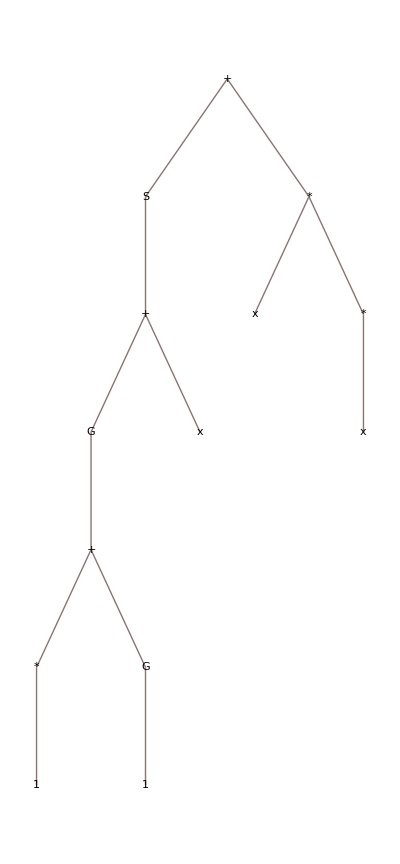
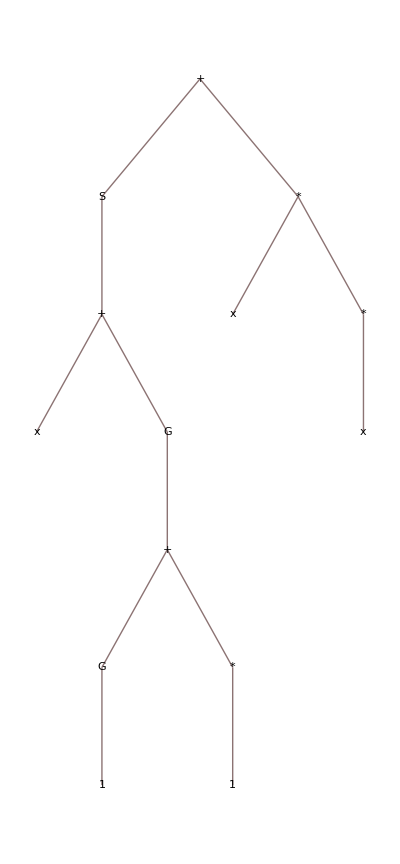
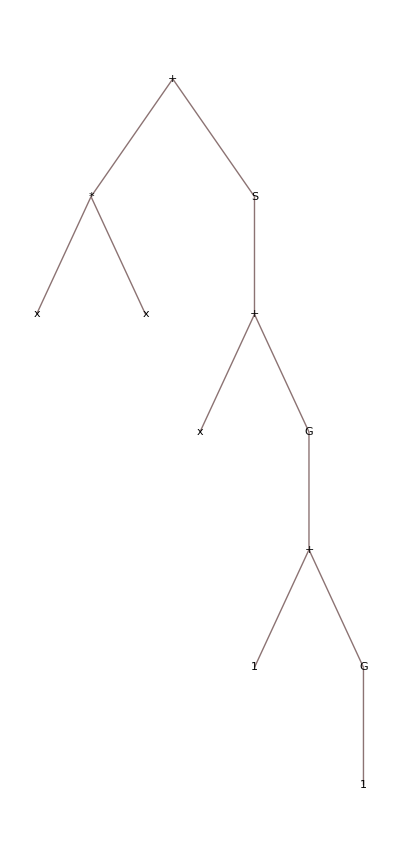
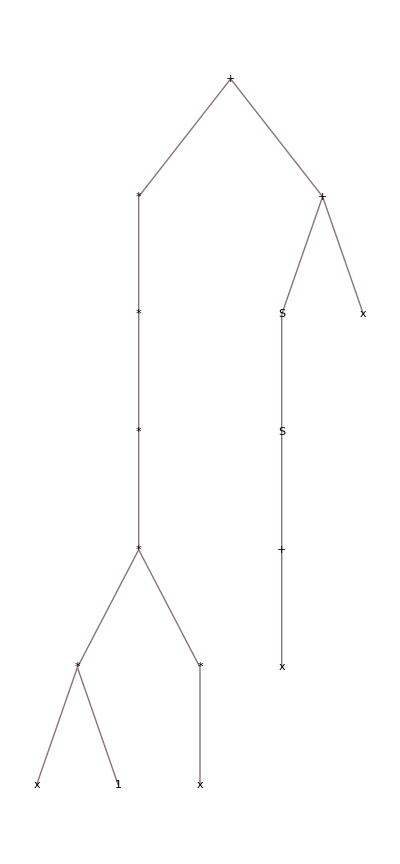
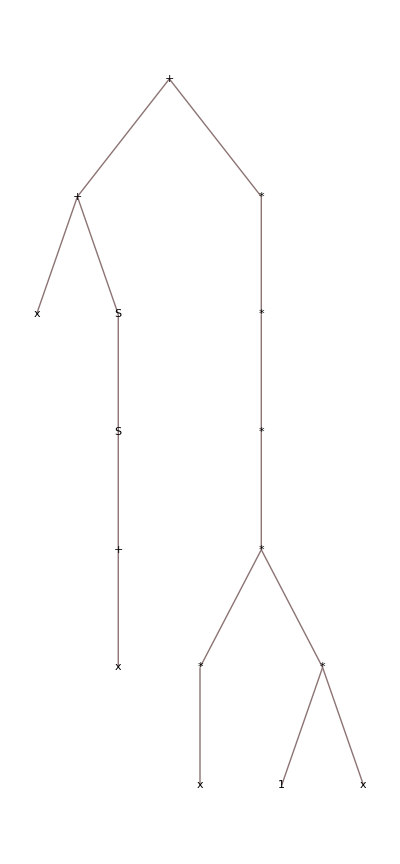
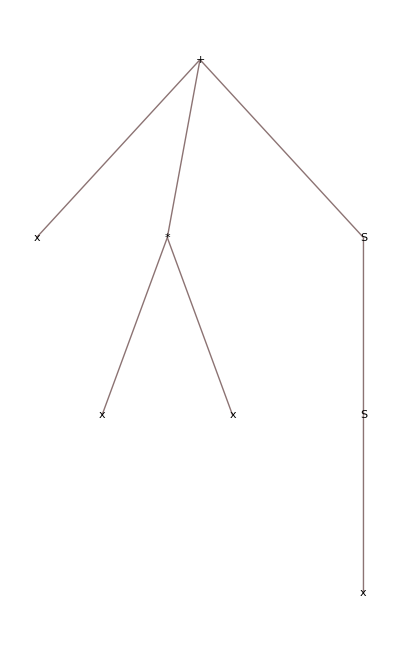
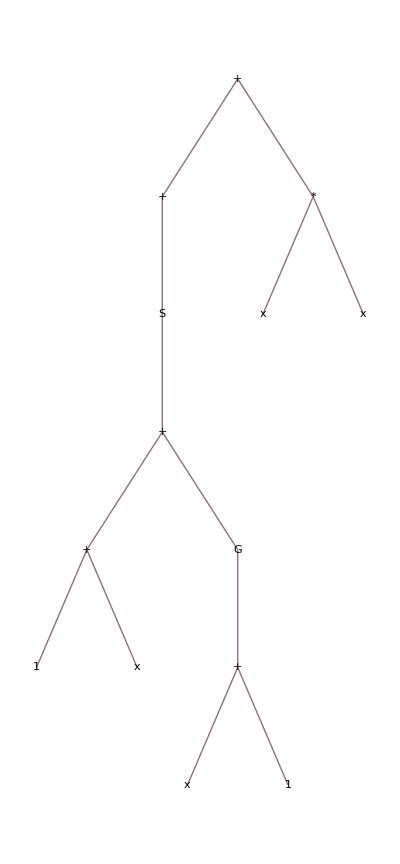
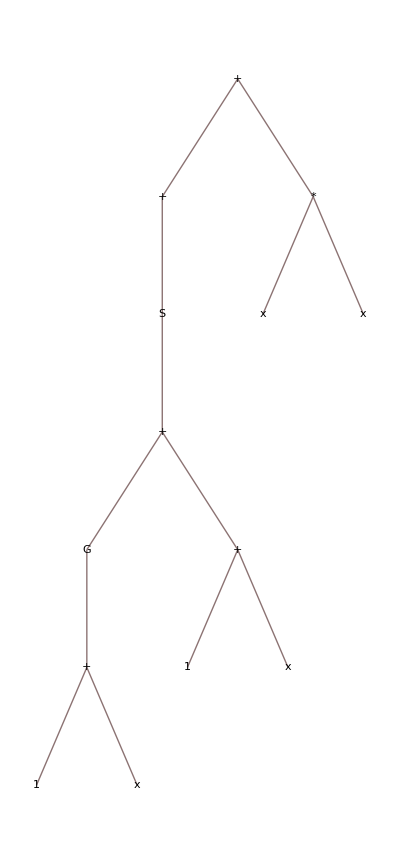
Gen | Genome | Sorted | Simplified | f
last | -Graphics- | -Graphics- | -Graphics- | 0.99656
last | -Graphics- | -Graphics- | -Graphics- | 0.983261
last | -Graphics- | -Graphics- | -Graphics- | 0.978954
last | -Graphics- | -Graphics- | -Graphics- | 0.978529
last | -Graphics- | -Graphics- | -Graphics- | 0.957386
last | -Graphics- | -Graphics- | -Graphics- | 0.956843
last | -Graphics- | -Graphics- | -Graphics- | 0.952837
last | -Graphics- | -Graphics- | -Graphics- | 0.951168
last | -Graphics- | -Graphics- | -Graphics- | 0.940757
last | -Graphics- | -Graphics- | -Graphics- | 0.852304

```mathematica
(res=sortConfigurationResults[sortedData,"A","BSF",10,Output->"BSFGenomes"]/.{x0->x})
```

```mathematica
Export["GP_H2.pdf",%]
```

GP_H2.pdf